Kaushik Chakram 
                                                                                                                     Professor Julia Kamenetzky
                                                                                                                     phys 425 &01
                                                                                                                     February 15,2018

1)Problem 2.7)a)

```mathematica
$Assumptions = {x,t,m,a,A,g,ω,ℏ,Subscript[A, 1],Subscript[A, 2],Subscript[A, 3],E2} ∈ Reals
```

(x|t|m|a|A|g|ω|ℏ|A_1|A_2|A_3|E2)∈Reals

```mathematica
F1[x_]= Piecewise[{{(A*x),0≤ x≤ a/2},{A*(a-x),a/2≤ x≤ a}}]
```

Piecewise[{{A x, 0≤x≤a/2}, {A (a-x), a/2≤x≤a}, {0, True}}]

Now if we set this expression equal to 1 and solve for A and take the positive root we get our normalization constant.

```mathematica
Integrate[(F1[x])^2,{x,0,a}]
```

Piecewise[{{(a^3 A^2)/12, a>0}, {0, True}}]

Let us redefine our piecewise with the normalization constant such that we can graph it to see if it matches.Let us call this new one F2[x_].

```mathematica
F2[x_]= Piecewise[{{((√(12/a^3))*x),0≤ x≤ a/2},{(√(12/a^3))*(a-x),a/2≤ x≤ a}}]
```

Piecewise[{{2 √3 √(1/a^3) x, 0≤x≤a/2}, {2 √3 √(1/a^3) (a-x), a/2≤x≤a}, {0, True}}]

We must set a to be something in order to graph it. Let a = 1.

```mathematica
a:=1
```

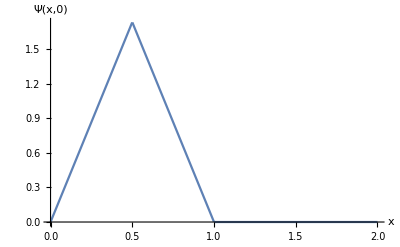

```mathematica
Plot[F2[x],{x,0,2}, AxesLabel->{x,"Ψ(x,0)"},AxesStyle->Directive[Black, 14]]
```

```mathematica
(*2.7part b) checking integration*)
$Assumptions ={n} ∈Integers
Integrate[(x)*(Sin[(n*π*x)/g]),{x,0,g/2}]
```

n∈Integers

-(g^2 (n π Cos[(n π)/2]-2 Sin[(n π)/2]))/(2 n^2 π^2)

```mathematica
Integrate[-1*(x)*(Sin[(n*π*x)/g]),{x,g/2,g}]
```

(g^2 (-n π Cos[(n π)/2]+2 ((-1)^n n π+Sin[(n π)/2])))/(2 n^2 π^2)

```mathematica
Integrate[(g)*(Sin[(n*π*x)/g]),{x,g/2,g}]
```

(g^2 ((-1)^(1+n)+Cos[(n π)/2]))/(n π)

```mathematica
Simplify[-(g^2 (n π Cos[(n π)/2]-2 Sin[(n π)/2]))/(2 n^2 π^2)+(g^2 (-n π Cos[(n π)/2]+2 ((-1)^n n π+Sin[(n π)/2])))/(2 n^2 π^2)+(g^2 ((-1)^(1+n)+Cos[(n π)/2]))/(n π)]
```

(2 g^2 Sin[(n π)/2])/(n^2 π^2)

```mathematica
Sum[1/((2*j)+1)^2,{j,0,Infinity}]
```

π^2/8

2)Problem 2.10)a) Just checking the integral for to obtain A_1 normalization constant.

```mathematica
F3[x_]:=((m*ω)/(π*ℏ))^(1/4)*ⅇ^((-m*ω*x^2)/(2*ℏ))
```

```mathematica
F4[x_]:=((Subscript[A, 1])/(√(2*ℏ*m*ω)))*(2*m*ω*x)*(F3[x])
```

```mathematica
Integrate[x^2*ⅇ^((-m*ω*x^2)/ℏ),{x,-∞,∞}]
```

ConditionalExpression[(√π)/(2 ((m ω)/ℏ)^(3/2)),m ω ℏ>0]

```mathematica
(*It works. The command below works too because we know ω ℏ and m positive non zero real numbers.*)
```

```mathematica
Integrate[Abs[F4[x]]^2,{x,-∞,∞}]
```

Piecewise[{{A_1^2, m ω ℏ>0}, {Integrate[(2 ⅇ^(-Re[(m x^2 ω)/ℏ]) Abs[(m x ω ((m ω)/ℏ)^(1/4) A_1)/(√(m ω ℏ))]^2)/(√π),{x,-∞,∞},Assumptions→(x|t|m|a|A|g|ω|ℏ|A_1|A_2)∈Reals&&m ω ℏ≤0], True}}]

```mathematica
(*Checking the integral to get normalization constant Subscript[A, 2]. We should get 1/(√(2!)). First define Piecewise for Subscript[ψ, 2](x).Again we know m,ω,ℏ are positive non-zero real numbers*)
F5[x_] := (Subscript[A, 2])*((2*m*ω*x^2)/ℏ - 1)*(F3[x])
```

```mathematica
Integrate[Abs[F5[x]]^2,{x,-∞,∞}]
```

Piecewise[{{2 A_2^2, m ω ℏ>0}, {Integrate[(ⅇ^(-Re[(m x^2 ω)/ℏ]) Abs[(-1+(2 m x^2 ω)/ℏ) ((m ω)/ℏ)^(1/4) A_2]^2)/(√π),{x,-∞,∞},Assumptions→(x|t|m|a|A|g|ω|ℏ|A_1|A_2)∈Reals&&m ω ℏ≤0], True}}]

Now we must declare the constants that we ha have in our functions to be able to graph those functions. I want to keep those equations in the same form so I shall use the following to declare constants. Let m be represented by b (m=b=1), (ω=c= 1),( and ℏ = d = 1). Now let us redefine those functions and I shall call these H[x].

```mathematica
H3[x_]:=((b*c)/(π*d))^(1/4)*ⅇ^((-b*c*x^2)/(2*d))
H4[x_]:=(1/(√(1!)))*(√((2*b*c)/d))*(x)*(H3[x])
H5[x_]:=(√(1/(2!)))*((2*b*c*x^2)/d - 1)*(H3[x])
```

```mathematica
(* Now let us declare the constants as planned and go for the plots.*)
b:=1
c:=1
d:=1
```

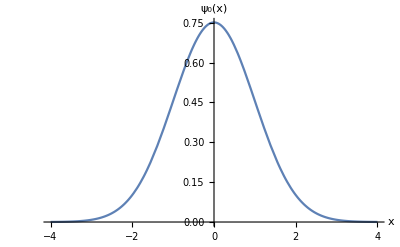

```mathematica
P3 =Plot[H3[x],{x,-4,4},  AxesLabel->{x,"ψ_0(x)"},AxesStyle->Directive[Black, 14]]
```

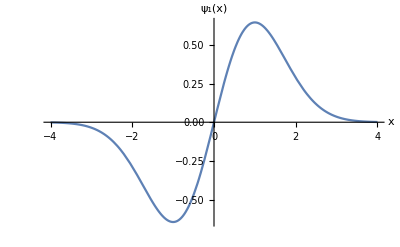

```mathematica
P4 =Plot[H4[x],{x,-4,4},  AxesLabel->{x,"ψ_1(x)"},AxesStyle->Directive[Black, 14]]
```

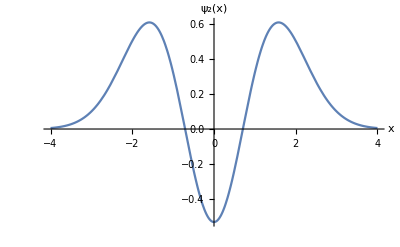

```mathematica
P5 = Plot[H5[x],{x,-4,4},  AxesLabel->{x,"ψ_2(x)"},AxesStyle->Directive[Black, 14]]
```

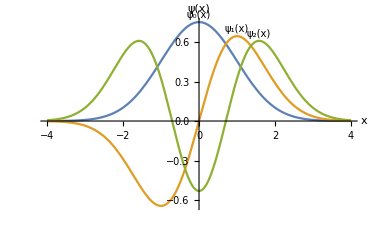

```mathematica
Plot[{H3[x],H4[x],H5[x]},{x,-4,4},PlotLabels-> Placed[{"ψ_0(x)","ψ_1(x)","ψ_2(x)"},Above],LabelStyle->Directive[Black, 10], AxesLabel->{x,"ψ(x)"},AxesStyle->Directive[Black, 12]]
```

2)Problem 2.10)part)c) Just checking the integrals such that we can show orthonormality. i will call these set of functions J[x].Again we know m,ω,ℏ are positive non-zero real numbers

```mathematica
J1[x_]:=(x)*(ⅇ^((-m*ω*x^2)/ℏ))
```

```mathematica
Integrate[J1[x],{x,-∞,∞}]
```

ConditionalExpression[0,m ω ℏ>0]

```mathematica
J2[x_]:=(x)^3*(ⅇ^((-m*ω*x^2)/ℏ))
Integrate[J2[x],{x,-∞,∞}]
```

ConditionalExpression[0,m ω ℏ>0]

3)Problem 2.11)a) Here we have to check a Whole Bunch of integral values.Let us define the same functions but now in terms of α and ξ (shortcut is esc x esc). We can call these functions K[x]. first let us declare the constant α and ξ.

```mathematica
α:= ((m*ω)/(π*ℏ))^(1/4)
ξ:=(√((m*ω)/ℏ))*(x)
K[ξ_]:=α*ⅇ^((-(ξ)^2)/2)
```

```mathematica
(*Just to check*)
Assuming[m *ω *ℏ>0,Integrate[Abs[K[ξ]]^2,{x,-∞,∞}]]
```

1

```mathematica
Integrate[(K[ξ])*ξ*(K[ξ]),{x,-∞,∞}]
```

ConditionalExpression[0,Re[(m ω)/ℏ]≥0]

```mathematica
ConditionalExpression[0,Re[(m ω)/ℏ]≥0]
(*I get that Mathematica is assuming different things for these codes, which is why I am getting  two different results, but how can I rectify this? Because the same function definition gave me the correct answers for the momentum expectation values.*)
```

```mathematica
Integrate[(K[ξ])*(ξ^2)*(K[ξ]),{x,-∞,∞}]
```

ConditionalExpression[1/2,Re[(m ω)/ℏ]>0]

```mathematica
Integrate[(Abs[K[ξ]]^2)*(ξ)^2,{x,-∞,∞}]
```

ConditionalExpression[(m ω √Abs[(m ω)/ℏ])/(2 ℏ Re[(m ω)/ℏ]^(3/2)),Re[(m ω)/ℏ]>0]

```mathematica
Integrate[(ℏ/ⅈ)*(K[ξ])*(D[K[ξ],x]),{x,-∞,∞}]
```

ConditionalExpression[0,Re[(m ω)/ℏ]≥0]

```mathematica
Integrate[(ℏ/ⅈ)^2*(K[ξ])*(D[K[ξ],{x,2}]),{x,-∞,∞}]
```

ConditionalExpression[(m ω ℏ)/2,Re[(m ω)/ℏ]>0]

```mathematica
(*Here weare defining Subscript[ψ, 1] interms of ξ and Subscript[ψ, 0](ξ)and checking normalization after that.*)
```

```mathematica
K1[ξ]:=√2*ξ*(K[ξ])
(*It works.*)Assuming[m *ω *ℏ>0,Integrate[Abs[K1[ξ]]^2,{x,-∞,∞}]]
```

1

```mathematica
(*checking expectation value of <x>*)Integrate[(K1[ξ]*ξ*K1[ξ]),{x,-∞,∞}]
```

ConditionalExpression[0,Re[(m ω)/ℏ]≥0]

```mathematica
Integrate[(K1[ξ]*(ξ)^2*K1[ξ]),{x,-∞,∞}]
```

ConditionalExpression[3/2,Re[(m ω)/ℏ]>0]

```mathematica
Integrate[(ℏ/ⅈ)*(K1[ξ])*(D[K1[ξ],x]),{x,-∞,∞}]
```

ConditionalExpression[0,Re[(m ω)/ℏ]≥0]

```mathematica
Integrate[(ℏ/ⅈ)^2*(K1[ξ])*(D[K1[ξ],{x,2}]),{x,-∞,∞}]
```

ConditionalExpression[(3 m ω ℏ)/2,Re[(m ω)/ℏ]>0]

Problem 4)2.13) part a)

```mathematica
E1[n_]:=(ℏ*ω)*(n+1/2)
Subscript[ψ, 0][x_]:=(1)*((m*ω)/(π*ℏ))^(1/4)*ⅇ^((-m*ω*x^2)/(2*ℏ))
Subscript[ψ, 1][x_]:=(√((2*m*ω)/ℏ))*x*(Subscript[ψ, 0][x])
Subscript[ψ, 2][x_] := (√(1/(2!)))*((2*m*ω*x^2)/ℏ - 1)*(Subscript[ψ, 0][x])
Ψ[x_,t_]:= (Subscript[A, 3])*(((3)*(Subscript[ψ, 0][x])*(ⅇ^(-ⅈ*((E1[0]*t)/ℏ))))+ ((4)*(Subscript[ψ, 1][x])*(ⅇ^(-ⅈ*((E1[1]*t)/ℏ)))) )
```

```mathematica
Integrate[(Ψ[x,0])*(Ψ[x,0]),{x,-∞,∞}] (*Note Capital E is a pre-defined function for exponent Do Not use E[]*)
```

ConditionalExpression[25 A_3^2,Re[(m ω)/ℏ]>0]

```mathematica
Subscript[Ψ, 1][x_,t_]:= (1/5)*(((3)*(Subscript[ψ, 0][x])*(ⅇ^(-ⅈ*((E1[0]*t)/ℏ))))+ ((4)*(Subscript[ψ, 1][x])*(ⅇ^(-ⅈ*((E1[1]*t)/ℏ)))) ) 
SuperStar[Subscript[Ψ, 1]][x_,t_]:= (1/5)*(((3)*(Subscript[ψ, 0][x])*(ⅇ^(+ⅈ*((E1[0]*t)/ℏ))))+ ((4)*(Subscript[ψ, 1][x])*(ⅇ^(+ⅈ*((E1[1]*t)/ℏ)))) ) 
Integrate[(ℏ/ⅈ)*(SuperStar[Subscript[Ψ, 1]][x,t])*(D[Subscript[Ψ, 1][x,t],{x,1}]),{x,-∞,∞}]
```

ConditionalExpression[-12/25 √2 √((m ω)/ℏ) ℏ Sin[t ω],Re[(m ω)/ℏ]>0]

Let m=ω=ℏ=1 and E_0= ℏω/2.

```mathematica
Integrate[(Subscript[ψ, 0][x])*(Subscript[ψ, 0][x]),{x,-√((2*1)/2),+√((2*1)/2)}]
```

```mathematica
Erf[√((m ω)/ℏ)] (*Reminder m=ω=ℏ=1*)
```

```mathematica
N[Erf[√1],6] (*where N numerical value function.*)
```

0.842701

```mathematica
Subscript[P, c]=(1-N[Erf[√1],6]) (* where Subscript[P, c] is the complement. *)
```

0.1573